```mathematica
sizes = {"8","10","12","14","16","18","20","22"}(*,"24","26","28","30","32"};*)
```

{8,10,12,14,16,18,20,22}

```mathematica
datas = Table[Import["C:\\Users\\jacks\\Documents\\GitHub\\cdt_rust\\data\\Volume_"<> s <>".csv"],{s,sizes}]
datas = Table[SortBy[data,-#[[2]]&],{data,datas}]
datas = Table[data[[;;,2]]-Mean[data[[;;,2]]],{data,datas}]
```

{{{1:1:2,4.5},{1:1:2,10.8},{1:1:2,3.6},{1:1:2,6.75},{1:1:2,9.9},9,{1:1:2,6.75},{1:1:2,3.6},{1:1:2,10.8},{1:1:2,4.5}},6,{1}}
 |  |  |  |

{{{1:1:2,10.8},{1:1:2,10.8},{1:1:2,9.9},{1:1:2,9.9},10,{1:1:2,3.6},{1:1:2,3.6},{1:1:2,3.6},{1:1:2,3.6}},6,{1}}
 |  |  |  |

{1}
 |  |  |  |

```mathematica
empiricalDistributions=Table[EmpiricalDistribution[data],{data,datas}];

(*Compute the CDF*)
cdfs=Table[CDF[empiricalDistribution,x],{empiricalDistribution,empiricalDistributions}];
```

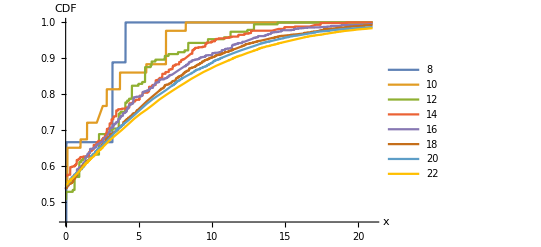

```mathematica
Plot[cdfs,{x,0,21},Exclusions->None,PlotStyle->Directive[Thick],AxesLabel->{"x","CDF"},PlotLegends->sizes]
```

```mathematica
data = datas[[4]];
```

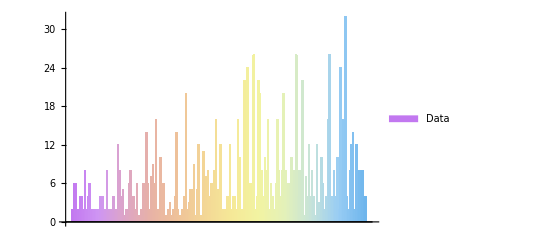

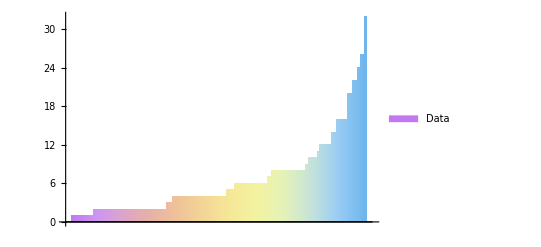

```mathematica
BarChart[Counts[data],ChartStyle->"Pastel",ChartLegends->{"Data"}]
BarChart[Sort[Counts[data]],ChartStyle->"Pastel",ChartLegends->{"Data"}]
```

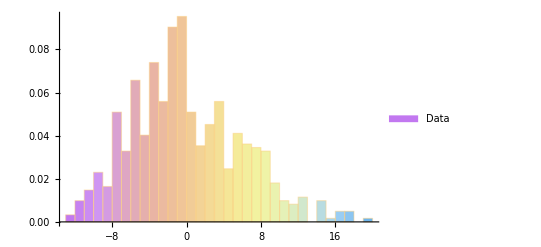

```mathematica
Histogram[data,{1},"Probability",ChartStyle->"Pastel",ChartLegends->{"Data"}]
```

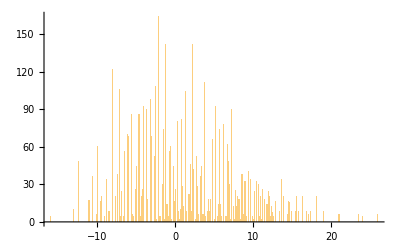

```mathematica
Histogram[data[[All,2]],{.01}]
```

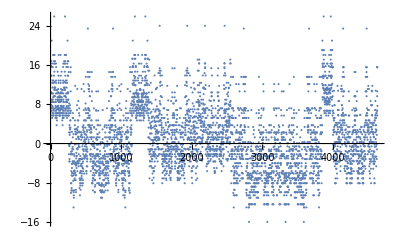

```mathematica
ListPlot[data[[All,2]]]
```

```mathematica
fit = Table[EstimatedDistribution[data, SkewNormalDistribution[c,v,s]],{data,datas}]
```

{SkewNormalDistribution[-4.57905,6.56205,1.80458],SkewNormalDistribution[-4.1082,5.58449,2.31222],SkewNormalDistribution[-5.99276,7.99384,2.57039],SkewNormalDistribution[-6.58337,8.87436,2.46119],SkewNormalDistribution[-7.23017,9.5922,2.69267],SkewNormalDistribution[-8.52487,11.3676,2.69484],SkewNormalDistribution[-9.34717,12.3904,2.89639],SkewNormalDistribution[-8.86752,11.9238,2.56929],SkewNormalDistribution[-10.1207,13.8077,2.32308],SkewNormalDistribution[-9.15341,12.4718,2.32049]}

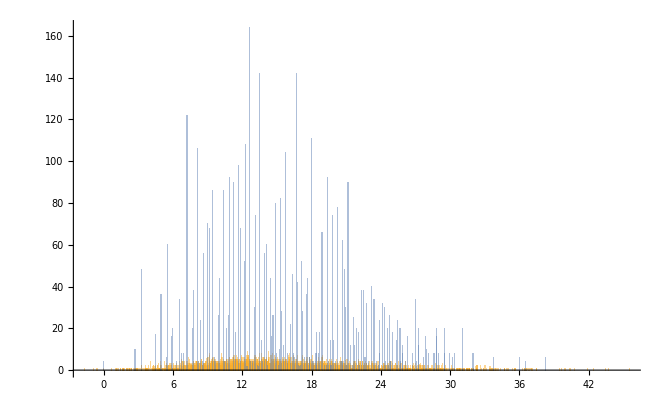

```mathematica
Histogram[{RandomVariate[fit,Length[data]],data},{.01}]
```

```mathematica
ℋ=DistributionFitTest[data,Automatic,"HypothesisTestData"];
ℋ["TestDataTable",All]
```

General::munfl: (1.04383×10^-293)/(1.08889×10^28) is too small to represent as a normalized machine number; precision may be lost.

| Statistic | P-Value
Anderson-Darling | 20.8609 | 0.
Baringhaus-Henze | 23.8788 | 9.11493×10^-14
Cramér-von Mises | 3.52386 | 0.
Jarque-Bera ALM | 148.707 | 0.
Mardia Combined | 148.707 | 0.
Mardia Kurtosis | -2.64596 | 0.008146
Mardia Skewness | 141.595 | 1.19247×10^-32
Pearson χ^2 | 1713.98 | 9.6×10^-322
Shapiro-Wilk | 0.98347 | 7.35978×10^-23

```mathematica
categoryCounts1=Counts[data[[All,1]]];
categoryCounts2=Counts[data[[-500;;,1]]];
barChart1=BarChart[Values[categoryCounts1],ChartLabels->Keys[categoryCounts1],ChartStyle->"Rainbow",ChartLegends->{"Count"},BarSpacing->Large,ImageSize->500];

barChart2=BarChart[Values[categoryCounts2],ChartLabels->Keys[categoryCounts2],ChartStyle->"Rainbow",ChartLegends->{"Count"},BarSpacing->Large,ImageSize->500];

Row[{barChart1,barChart2}]
```